```mathematica
(*generation of the phase distribution to be used in the calculation of the field components*)
ArcTan[0,0]:=0;
n=10;
m=10;
k=1; alpha=0.4;
For[i=1;t=x,i^1<n-1,i++,t=i^1+0;
For[j=1;tt=y,j^1<m-1,j++,tt=j+0;{ss=Table[k*Sin[alpha]*√(i^2+j^2),{i,Range[-5,5,0.1]},{j,Range[-5,5,0.1]}]}]];
```

SetDelayed::write: Tag ArcTan in ArcTan[0, 0] is Protected.

```mathematica
(*Trapezoid Rule*)
n=10;S0=0;u=2;alpha=0.4;S1=0;S2=0;
x=ss;RHO=0;ZI=0
For[i=1;p=x,i^1<n,i++,p=x^1;{aa=Table[RHO=RHO+(Cos[i*alpha/n])^(1/2) Sin[2*i*alpha/n]*1/Sin[i*alpha/n]*BesselJ[1,(p*Sin[i*alpha/n]/Sin[1.3])] Exp[(Cos[i*alpha/n])*(I+u)/(Sin[alpha])^2],{i,n}],
bb=Table[ZI=ZI+(Cos[i*alpha/n])^(1/2)(Sin[2*i*alpha/n])^(2)*1/Sin[i*alpha/n]*BesselJ[0,(p*Sin[i*alpha/n]/Sin[1.3])] Exp[(Cos[i*alpha/n])*(I+u)/(Sin[alpha])^2],{i,n}]}]
```

0

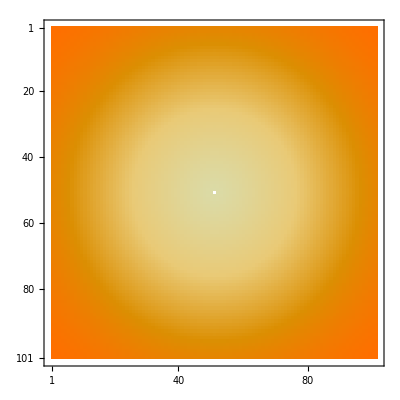

```mathematica
RHO=(alpha/n)*(RHO+0.5*(Cos[alpha]^0.5)*Sin[2*alpha]*(1/Sin[alpha])*BesselJ[1,ss]*Exp[Cos[alpha]*(I+u)/(Sin[alpha])^2]);

ZI=(2*I*alpha/n)*(ZI+0.5*(Cos[alpha]^0.5)*Sin[alpha]^2*(1/Sin[alpha])*BesselJ[0,ss]*Exp[Cos[alpha]*(I+u)/(Sin[alpha])^2]);


MatrixPlot[RHO]
```

```mathematica
ENRHO=Abs[RHO]^2+Abs[ZI]^2
```

{{2.83558×10^12,2.84264×10^12,2.8496×10^12,2.85643×10^12,2.86315×10^12,2.86975×10^12,2.87622×10^12,2.88257×10^12,2.8888×10^12,2.89489×10^12,2.90086×10^12,«80»,2.89489×10^12,2.8888×10^12,2.88257×10^12,2.87622×10^12,2.86975×10^12,2.86315×10^12,2.85643×10^12,2.8496×10^12,2.84264×10^12,2.83558×10^12},«99»,{«1»}}

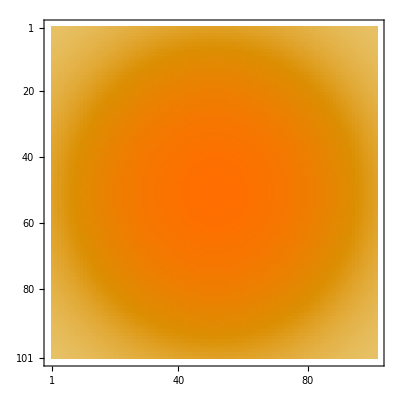

```mathematica
MatrixPlot[Abs[ZI]^2]
```